## Chapter 2: Multiple Buildings and Complex Campuses

### Overview

In the first chapter we built a simple application to track the energy consumption of a single building using multiple fuel sources.  This is the obvious place to start, and it will work for many schools.  Of course, many schools have several buildings,  and many schools will find more complex metering scenarios.  You may find meters that measure the consumption of multiple buildings, and meters for loads not connected to a building.  For instance, I happen to live on a boarding school campus.  On that campus there are many buildings with their own meters, one building with two meters, and in the center of campus there is a single large transformer with a meter that serves several large academic buildings that do not have individual meters.  There are also meters not on buildings, but on  water pumps and parking lot lights.  There is similar complexity with regard to heating fuel, where there is a central plant that burns wood chips to heat much of the campus, but a number of buildings have their own boilers that use fuel oil or propane.

## An Introduction to Entities

The Wolfram Language’s provides a number of data structures that can be used to represent entities of interest.  Much of the language’s built in knowledge is represented as built in Entities.  You can find build in information for everything from famous buildings to famous battles.

An easy way to begin exploring the language’s built in knowledge is to use natural language search capabilities.  You can start by entering ctr =  as in the line below.  You can then enter the name of an entity that you are interested in and press Enter.  If the language can identify what you are interested in an Entity will be returned as below.

```mathematica
LinguisticAssistant_□
```

Alternatively, you can specify the Entity using code if you know it’s Type and Name.

```mathematica
Entity["Building", "EmpireStateBuilding"]
```

Empire State Building

If you  want to know what properties are available for an entity you can use the code below.

```mathematica
Entity["Building","EmpireStateBuilding::h583b"]["Properties"]
```

{administrative region,architect,architectural height,style,firm,city location,clients,construction cost,completion date,construction start date,construction status,coordinates,country,destruction date,elevation,number of elevators,engineers,entity classes,floors,floor area,ground breaking date,total height,image,latitude,longitude,material,name,opening date,position,renovation date,roof height,number of rooms,seating capacity,structural engineer,structural system}

You can also retrieve an Entity’s properties and their values as below.

```mathematica
EntityValue[Entity["Building","EmpireStateBuilding::h583b"],"PropertyAssociation"]
```

<|administrative region→{New York County (Manhattan), New York, United States,New York, United States},architect→{William F. Lamb},architectural height→1250. ft,style→{Art Deco,Streamline Moderne},firm→{Shreve, Lamb & Harmon},city location→{New York City},clients→Missing[NotAvailable],construction cost→6.76293633e8 $,completion date→Year: 1931,construction start date→Year: 1929,construction status→completed,coordinates→{40.7484,-73.9857},country→{United States},destruction date→Missing[NotAvailable],elevation→Missing[NotAvailable],number of elevators→73,engineers→Missing[NotAvailable],entity classes→{seven wonders of the modern world,skyscrapers,{city, {newyork, newyork, unitedstates}},completed buildings,{country, unitedstates},{person, williamflamb::3rf3y},{uscounty, newyorkny},{usstate, newyork}},floors→102,floor area→2.24835×10^6 ft^2,ground breaking date→Missing[NotAvailable],total height→1250. ft,image→-Graphics-,latitude→40.7484 °,longitude→-73.9857 °,material→Missing[NotAvailable],name→Empire State Building,opening date→Day: Fri 1 May 1931,position→GeoPosition[{40.7484,-73.9857}],renovation date→Missing[NotAvailable],roof height→1250. ft,number of rooms→Missing[NotAvailable],seating capacity→Missing[NotAvailable],structural engineer→{Homer Gage Balcom},structural system→Missing[NotAvailable]|>

What is returned above is an Association of Properties and their Values.  If you want to view the information in a tabular format you can wrap the expression in a Dataset.

```mathematica
Dataset[EntityValue[Entity["Building","EmpireStateBuilding::h583b"],"PropertyAssociation"]]
```

Dataset[<>]

## Defining your own Entities

It is possible to define your own entities i

## Defining our Data Model

Since our application needs to work for school campuses with this kind of complexity we need to step back, and put some thought into how we want to represent the world within the application.  We need to define our data model.

```mathematica
TextSentences[WikipediaData["data model"]][[;;5]]
```

{A data model (or datamodel) is an abstract model that organizes elements of data and standardizes how they relate to one another and to the properties of real-world entities.,For instance, a data model may specify that the data element representing a car be composed of a number of other elements which, in turn, represent the color and size of the car and define its owner.,The term data model can refer to two distinct but closely related concepts.,Sometimes it refers to an abstract formalization of the objects and relationships found in a particular application domain: for example the customers, products, and orders found in a manufacturing organization.,At other times it refers to the set of concepts used in defining such formalizations: for example concepts such as entities, attributes, relations, or tables.}

To define our data model we need to ask what objects does our application need to represent, what are the attributes of those objects that we need to represent, and how are those objects related to each other.  Of particular interest for this application is the question of to which object within the application we will associate energy consumption values.

So far we have identified meters, transformers, campus buildings of multiple types, and a biomass boiler.  There will be other types of objects to wrestle with, but this is sufficient to think things through.

I like to use the Wolfram Language’s Graph functionality to visualize objects and how they are related.  The first thing to do is to set the shapes that will be used for each vertex.The code below sets the left hand value to be equal to the first result of the WebImageSearch.

```mathematica
transformer=Take[WebImageSearch["electrical transformer"],1];
```

```mathematica
academicBuilding=Take[WebImageSearch["academic building"],1];
```

```mathematica
biomassBoiler=Take[WebImageSearch["biomass boiler"],1];
```

```mathematica
diningHall=Take[WebImageSearch["dining hall"],1];
```

```mathematica
meter=Take[WebImageSearch["electric meter"],1];
```

The code below defines a graph that describes the relationships between electrical meters, transformers, buildings, and a central biomass boiler.  It uses the values set by the code above to define the VertexShape for each vertex.

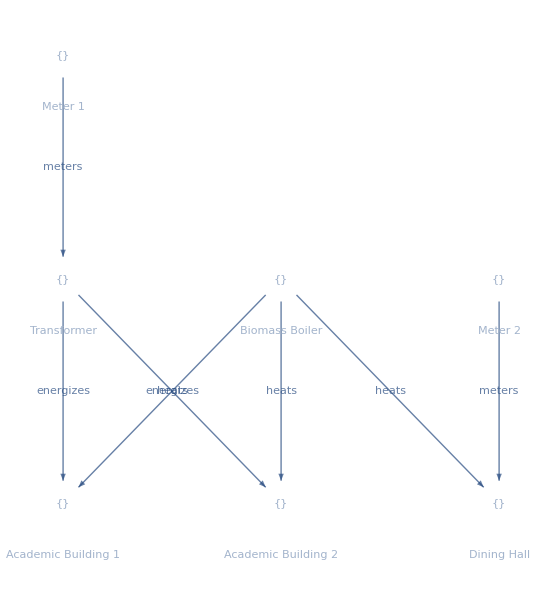

```mathematica
Graph[
{
Labeled["Transformer"->"Academic Building 1","energizes"],
Labeled["Transformer"->"Academic Building 2","energizes"],
Labeled["Biomass Boiler"->"Academic Building 1","heats"],
Labeled["Biomass Boiler"->"Academic Building 2","heats"],
Labeled["Meter 1"->"Transformer","meters"],
Labeled["Biomass Boiler"->"Dining Hall","heats"],
Labeled["Meter 2"->"Dining Hall","meters"]
},
VertexShape->{"Transformer"->transformer,"Academic Building 1"->academicBuilding,"Academic Building 2"->academicBuilding,
"Biomass Boiler"->biomassBoiler,
"Dining Hall"->diningHall,
"Meter 1"->meter,
"Meter 2"->meter},
VertexSize->0.2,
VertexLabels->Placed["Name",Below]]
```

In deciding on our data model we need to allow sufficient complexity to accurately represent the world but not introduce so much complexity that it makes working with the application unwieldy.  For instance, we may not need to include meters in our data model.  Associating the consumption of a commodity measured by a meter with the meter might provide the most accurate representation of the world, but for our purposes the consumption of the commodity is done by the buildings on campus.  So, for now, we will omit meters from our data model.  While we will omit meters, we don’t want to overly simplify the model so that it only includes the buildings.

## Introducing Entities

The Wolfram Language

#### Campus Buildings

Campus Buildings will often have their own points of delivery for each commodity consumed, however on many campuses it is common for many buildings to share points of delivery, for example where an electric utility places a meter on a transformer that provides power to multiple buildings.

#### Points of Delivery

Points of Delivery, sometimes referred to Service Delivery Points, or Service Point Locations are the point at which a commodity is delivered from the  supplier to the  customer.  In the case of electricity supply, the Point of Delivery is typically the point at which the utility places a meter that measures electrical consumption by the customer.  In the case of fuel oil deliveries it would be the fill tube of the customer’s fuel tank.  In this case the measurement of the quantity delivered is done by a meter on the fuel oil truck, not by a meter installed at the customer’s facility.  Points of Delivery often supply a single building with an  commodity, although in many instances a point of delivery may supply many buildings, such as delivery of wood chips to a biomass boiler that heats many buildings on campus.  In some cases a Point of Delivery may not have any association with a building, such as metered street lights or water pumps.  It is for these reasons of multiple buildings being served by a single service delivery point, or a service delivery point having no building at all, that we require a concept distinct from campus buildings to associate measured quantities to.

#### Measured Quantities

There are a few flavors of measured quantities whose differences arise from different delivery and metering technologies.  In most cases a single quantity will be associated to a Point of Delivery, however electrical meters often measure multiple distinct units of measure, and often in two directions when a generator is installed behind the meter so that electricity is at times

## Entering Master Data

```mathematica
TextSentences[WikipediaData["master data"]][[;;5]]
```

{Master data represents the business objects that contain the most valuable, agreed upon information shared across an organization.,It can cover relatively static reference data, transactional, unstructured, analytical, hierarchical and metadata.,It is the primary focus of the information technology (IT) discipline of master data management (MDM).,Master data is usually non-transactional in nature, but in some cases gray areas exist where transactional processes and operations may be considered master data by an organization.,For example, master data may contain information about customers, products, employees, materials, suppliers, and vendors.}

Buildings and Points of Delivery are the  master data objects of interest to a campus energy management project.  By collecting and maintaining accurate master data you will be able to perform analyses that go far beyond what is possible with collecting energy consumption data alone.  For instance, if you have access to accurate information regarding the floor area of each building on campus, you will be able to calculate the energy intensity of each building.  If you include each building’s function, such as athletic facility, dormitory, administrative building you will be able to determine how much each function contributes to your school’s energy consumption.  
There are several possible methods of building a master data repository with the Wolfram Language.  This project is using the language’s EntityStore functionality.  If you wish, one can enter master data by brute force, and fully compose the code for each entry.  It is also possible to use the Language’s form building capabilities to construct a form to facilitate data entry.